(-0.5 ⅇ^(-0.7 z3)-0.6106 (1-0.5 ⅇ^(-0.7 z3))-ω | (0.609642 (1-0.5 ⅇ^(-0.7 z3)) (0.5 ⅇ^(-0.7 zres2)+0.6106 (1-0.5 ⅇ^(-0.7 zres2))))/(1-0.5 ⅇ^(-0.7 zres2))
0.36636 (1-0.5 ⅇ^(-0.7 z3)) (1-0.1 ω) | -0.241933 (1-0.5 ⅇ^(-0.7 z3))-ω)

(-0.5 ⅇ^(-0.7 z2)-0.6106 (1-0.5 ⅇ^(-0.7 z2))-ϕ | (0.660369 (1-0.5 ⅇ^(-0.7 z2)) (0.5 ⅇ^(-0.7 zres3)+0.6106 (1-0.5 ⅇ^(-0.7 zres3))))/(1-0.5 ⅇ^(-0.7 zres3))
0.36636 (1-0.5 ⅇ^(-0.7 z2)) (1-0.1 ϕ) | -0.223348 (1-0.5 ⅇ^(-0.7 z2))-ϕ)

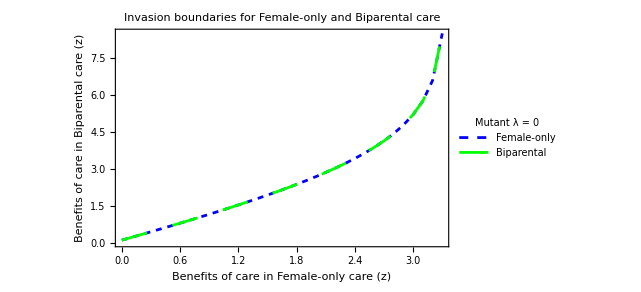

```mathematica
(*BASELINES*)
em0=0.5;
ef0 = 1-em0;

mum0=0.5;
muf0= 0.5;

sigjm0=0.6;
sigjf0=0.6;
taum0=0.1;
tauf0=0.1;

mm0=0.5;
mf0=0.5;

k0=250;
rr0=6;
wm0=0.4;
wf0=0.4;

z0=1;
(*_________________________________________________________________________*)
(*RESIDENTS*)


(*Female only*)
emres2=em0;
efres2 =1-emres2;

(*zres = z0;*)
cmres2 = 0.0;
cfres2 = 0.7;
ctres2 = cmres2+cfres2;

mumres2=mum0*E^(-zres2*ctres2);
mufres2=muf0*E^(-zres2*ctres2);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres2=1-((1-mm0)*E^(-((1-mum0)*emres2)));
mfres2=1-((1-mf0)*E^(-((1-muf0)*efres2)));
KR2=k0;
rres2=rr0*E^(-((1-mum0)*emres2+((1-muf0)*efres2))/2);

wmres2=1-((1-wm0)*E^(-cmres2));
wfres2= 1-((1-wf0)*E^(-(efres2*(1-muf0)+(1-mum0)*emres2+cfres2)));

emmres2 = emres2*(1-mumres2)*mmres2;
emfres2 = efres2* (1-mufres2)*mfres2;
esmres2= emres2*(1-mumres2);
esfres2 = efres2* (1-mufres2);
amres2 = emres2*(1-mumres2)*mmres2*sigjmres;
afres2 = efres2* (1-mufres2)* mfres2*sigjfres;

AR2 =KR2*(1-((wmres2*amres2+wfres2*afres2)*(mumres2*emres2 + mufres2*efres2 + mmres2*esmres2 + mfres2*esfres2)/((emmres2*sigjmres+emfres2*sigjfres)*rres2*afres2)));



(*Biparental*)
emres3=em0;
efres3 =1-emres3;

(*zres3 = z0;*)
cmres3 = 0.35;
cfres3=0.35;
ctres3 = cmres3+cfres3;

mumres3=mum0*E^(-zres3*ctres3);
mufres3=muf0*E^(-zres3*ctres3);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres3=1-((1-mm0)*E^(-((1-mum0)*emres3)));
mfres3=1-((1-mf0)*E^(-((1-muf0)*efres3)));
KR3=k0;
rres3=rr0*E^(-((1-mum0)*emres3+((1-muf0)*efres3))/2);

wmres3=1-((1-wm0)*E^(-cmres3));
wfres3= 1-((1-wf0)*E^(-(efres3*(1-muf0)+(1-mum0)*emres3+cfres3)));

emmres3 = emres3*(1-mumres3)*mmres3;
emfres3 = efres3* (1-mufres3)*mfres3;
esmres3= emres3*(1-mumres3);
esfres3 = efres3* (1-mufres3);
amres3 = emres3*(1-mumres3)*mmres3*sigjmres;
afres3 = efres3* (1-mufres3)* mfres3*sigjfres;

AR3 =KR3*(1-((wmres3*amres3+wfres3*afres3)*(mumres3*emres3 + mufres3*efres3 + mmres3*esmres3 + mfres3*esfres3)/((emmres3*sigjmres+emfres3*sigjfres)*rres3*afres3)));



(*___________________________________________________*)
(*MUTANTS*)


(*Female only care*)
(*z=0;*)
cm2=0.0;
cf2=0.7;
ct2 = cm2 + cf2;
ct2;
em2=em0;
ef2 = 1-em2;

mum2=mum0*E^(-z2*ct2);
muf2=muf0*E^(-z2*ct2);

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm2=1-((1-mm0)*E^(-((1-mum0)*em2)));
mf2=1-((1-mf0)*E^(-((1-muf0)*ef2)));

k=k0;
rr2=rr0*E^(-((1-mum0)*em2+((1-muf0)*ef2))/2);

wm2=1-((1-wm0)*E^(-cm2));
wf2=1-((1-wf0)*E^(-(ef2*(1-muf0)+(1-mum0)*em2 +cf2)));

emm2 = em2*(1-mum2)*mm2;
emf2 = ef2* (1-muf2)*mf2;
esm2 = em2*(1-mum2);
esf2 = ef2*(1-muf2);
am2 = em2*(1-mum2)*mm2*sigjm;
af2 = ef2* (1-muf2)* mf2*sigjf;


(*Biparental care*)
(*z=z0;*)
cm3=0.35;
cf3=0.35;
ct3 = cm3 + cf3;
ct3;

em3=em0;
ef3=1-em3;

mum3=mum0*E^(-z3*ct3);
muf3=muf0*E^(-z3*ct3);

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm3=1-((1-mm0)*E^(-((1-mum0)*em3)));
mf3=1-((1-mf0)*E^(-((1-muf0)*ef3)));

wm3=1-((1-wm0)*E^(-cm3));
wf3=1-((1-wf0)*E^(-(ef3*(1-muf0)+(1-mum0)*em3 +cf3)));

emm3 = em3*(1-mum3)*mm3;
emf3 = ef3* (1-muf3)*mf3;
esm3 = em3*(1-mum3);
esf3 = ef3*(1-muf3);

k=k0;
rr3=rr0*E^(-((1-mum0)*em3+((1-muf0)*ef3))/2);

am3 = em3*(1-mum3)*mm3*sigjm;
af3 = ef3* (1-muf3)* mf3*sigjf;



(*INVASION MATRICIES*)


(*Invading FEMALE only care*)

(*Biparental mutant *)
a3=-(mum3*em3+muf3*ef3+mm3*esm3+mf3*esf3);
b32 = rr3*af3*(1-(AR2/k));
c3=emm3*sigjm*(1-ω*taum)+emf3*sigjf*(1-ω*tauf);
d3 = -(wm3*am3+wf3*af3);
mat32={{-ω+a3,b32},{c3,-ω+d3}};
MatrixForm[mat32]
ans32=Solve[Det[mat32]==0,ω];
res32=Max[ω/.ans32];




(*Female only mutant*)
a2=-(mum2*em2+muf2*ef2+mm2*esm2+mf2*esf2);
b23 = rr2*af2*(1-(AR3/k));
c2=emm2*sigjm*(1-ϕ*taum)+emf2*sigjf*(1-ϕ*tauf);
d2 = -(wm2*am2+wf2*af2);
mat23={{-ϕ+a2,b23},{c2,-ϕ+d2}};
MatrixForm[mat23]
ans23=Solve[Det[mat23]==0,ϕ];
res23=Max[ϕ/.ans23];


resMiF=Table[zres2=0.0+i/10;jo=
FindRoot[{res32==0},{z3,1,3}];{zres2,z3/.jo},{i,0,33}];

(*Flip*)
resFiMflip=Table[z2=0.0+i/10;jo=
FindRoot[{res23==0},{zres3,0,3}];{z2,zres3/.jo},{i,0,33}];


ListPlot[{Re[resFiMflip],Re[resMiF]},
Joined -> {True, True},
Frame -> {True,True, False, False},
PlotLegends->LineLegend[{"Female-only","Biparental"},
LegendLabel-> "Mutant λ = 0",
LegendMarkerSize->{20,20},
LabelStyle ->{FontSize->16}, LegendMargins ->5
],
FrameLabel->{Row[{Style["Benefits of care in",Black, 18], Style[" Female-only",Blue, 18], Style[ " care (z)",Black, 18]}],Style[Rotate[Column[{"Benefits of care in",Row[{Style["Biparental",Green], Style[" care", Black]}],"(z)   "},Alignment-> Center], 270 Degree],18]},LabelStyle ->Black,
PlotLabel-> Style[Column[{"Invasion boundaries for"," Female-only and Biparental care", " "}, Alignment ->Center],22],LabelingSize->350,
ImageSize-> 600,
PlotStyle  -> {{ Blue, Dashing[0.009]},{Green,Dashing[0.04]}}
]


(*,Dashing[0.009], Dashing[0.03]*)
```